```mathematica
SetDirectory[NotebookDirectory[]];
baseImg=-Graphics-;
img1 = -Graphics-;img2=-Graphics-;
```

## Position einer Person - Schwieriger

Die Hand einer Person wird gefunden indem die Person selbst abgeschnitten wird. Zuerst wird nach der Person gesucht. Dies geschieht über das Differenbild zu einer Basis.

```mathematica
cutBase = ImageTrim[baseImg, {{0,0},{640,50}}]
cutImg1= ImageTrim[img1, {{0,0},{640,50}}]
```

-Graphics-

-Graphics-

```mathematica
diff1=ImageDifference[cutBase,cutImg1]
```

-Graphics-

```mathematica
cutImage=MedianFilter[Binarize[diff1,FindThreshold[diff1]*2],2]
```

-Graphics-

### Umrandung der Person finden

Die weissen Flächen sollten nach den vorigen Schritten nur noch die Bewegung der Person abbilden.Um die restliche Person von der Suche nach den Armen ausnehmen zu können, versuchen wir die Ränder der Person zu finden. Vorerst wird dazu einfach Minimum und Maximum verwendet. Falls das Bild links oder rechts von der Person noch rauschen enthält, ist das Resultat unbrauchbar.

```mathematica
whites=ImageValuePositions[cutImage,White];
corners=Transpose[{
Through[{Min,Max}[First/@whites]],
Through[{Min,Max}[Last/@whites]]}];
Show[cutImage,Graphics[{EdgeForm[Directive[Thick,Dashed,Red]],Transparent,Rectangle[corners[[1]],corners[[2]]]}]]
```

-Graphics-

```mathematica
leftBottom={corners[[1,1]],0};
rightBottom={corners[[2,1]],0};
Show[img1,Graphics[{PointSize[Large],Red,Line[{{leftBottom[[1]],480},{leftBottom[[1]],0}}]}],
Graphics[{PointSize[Large],Red,Line[{{rightBottom[[1]],480},{rightBottom[[1]],0}}]}]]
```

-Graphics-

### Scanne die Kolonne, wo die Hand sein müsste auf dem Diffbild

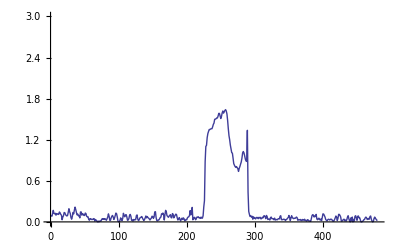

```mathematica
(*10% Zuschlag*)
col = Round[rightBottom[[1]]+0.1*(rightBottom[[1]]-leftBottom[[1]])] ;
diffCol=Abs[ImageData[img1][[All,col]]-ImageData[baseImg][[All,col]]];
ListLinePlot[Total[diffCol,{2}],PlotRange->{{0,480},{0,3}}]
```

Der Bereich mit der höchsten Differenz ist der Schatten des Arms. Der Bereich mit der zweithöchsten ist der Arm selbst. Noch ist unklar, ob sich dieses Pattern durch alle möglichen Präsentationssituationen zieht.

#### Visualisiere auch noch die nächsten Kolonnen nach Helligkeit

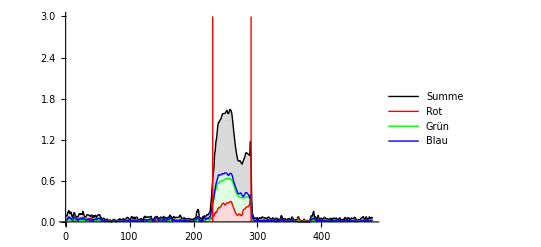

-Graphics-

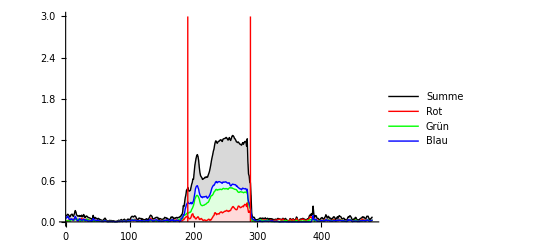

-Graphics-

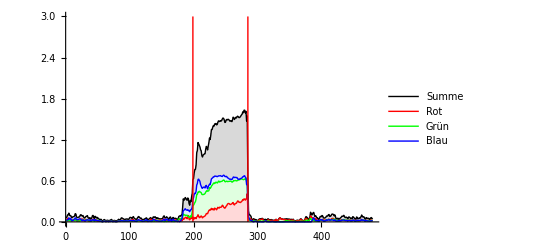

-Graphics-

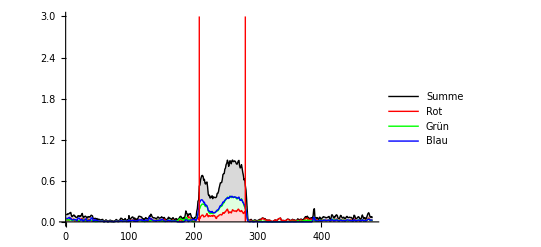

-Graphics-

First::first: {} has a length of zero and no first element.

Part::partw: Part 1 of {} does not exist.

Last::nolast: {} has a length of zero and no last element.

Part::partw: Part 1 of {} does not exist.

-Graphics-

-Graphics-

```mathematica
columnDifferences[baseImgParam_,frameImgParam_,colsParam_]:=Module[
{colTotals={},meanCols,blobBegin,blobEnd,blobCenter,
channelR={},channelG={},channelB={}},
For[i=1,i≤Length[colsParam],i++,
diffCols=Abs[ImageData[baseImgParam][[All,colsParam[[i]]]]
-ImageData[frameImgParam][[All,colsParam[[i]]]]];
(* sum up color channels *)
colTotals=Append[colTotals,Total[diffCols,{2}]];
(* color difference *)
channelR=Append[channelR,Flatten[Take[diffCols,All,1]]];
channelG=Append[channelG,Flatten[Take[diffCols,All,2;;2]]];
channelB=Append[channelB,Flatten[Take[diffCols,All,-1]]];
];

meanCols=Mean[colTotals];
blobBegin=Position[meanCols,First@Select[meanCols,#>0.5&]][[1,1]];
blobEnd=Position[meanCols,Last@Select[meanCols,#>0.5&]][[1,1]];
blobCenter = blobBegin+(blobEnd-blobBegin)/2;

Print[Show[
ListLinePlot[{
Mean[colTotals],
Mean[channelR],Mean[channelG],Mean[channelB]
},
PlotRange->{{0,480},{0,3}},
Filling->{
1->{Axis,LightRed},
2->{{1},LightGray},
3->{{2},LightGreen},
4->{{3},LightBlue}
},
PlotLegends->{"Summe","Rot","Grün","Blau"},
PlotStyle->{Black,Red,Green,Blue}],
Graphics[{PointSize[Large],Red,Line[{{blobBegin,0},{blobBegin,3}}]}],
Graphics[{PointSize[Large],Red,Line[{{blobEnd,0},{blobEnd,3}}]}]
]];

Print[Show[
frameImgParam,
Graphics[{PointSize[Small],Red,Point[{Median[colsParam],blobCenter}]}]
]];

colTotals
]
columnDifferences[baseImg,img1,Range[col,col+10,2]];
columnDifferences[baseImg,img1,Range[col+20,col+30,2]];
columnDifferences[baseImg,img1,Range[col+30,col+40,2]];
columnDifferences[baseImg,img1,Range[col+40,col+50,2]];
columnDifferences[baseImg,img1,Range[col+50,col+60,2]];
```

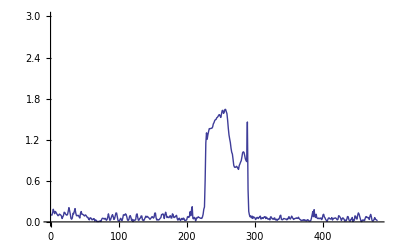

```mathematica
ListLinePlot[stripeArmPositions,PlotRange->{{0,480},{0,3}}]
```

### Position einer Hand

```mathematica
ImageDifference[baseImg,img2]
```

-Graphics-

```mathematica
armCut= ImageCrop[diffMed,{640-rightBottom[[1]],Full},Left]
```

ImageCrop::imginv: Expecting an image or graphics instead of diffMed.

ImageCrop[diffMed,{470.5,Full},Left]

### Äussersten Punkt des Armes finden

```mathematica
armWhites=ImageValuePositions[armCut,White];
maxX=(Max/@Transpose[armWhites])[[1]];
meanMaxX=Mean[Select[armWhites,#[[1]]≥ maxX&]]
HighlightImage[armCut,{meanMaxX},Method->{"DiskMarkers",3}]
```

ImageValuePositions::imginv: Expecting an image or a graphics instead of ImageCrop[diffMed, {470.5, Full}, Left].

ImageValuePositions::argt: ImageValuePositions called with 0 arguments; 2 or 3 arguments are expected.

Mean[ImageValuePositions[]]

HighlightImage::imginv: Expecting an image or graphics instead of ImageCrop[diffMed, {470.5, Full}, Left].

HighlightImage[ImageCrop[diffMed,{470.5,Full},Left],{Mean[ImageValuePositions[]]},Method→{DiskMarkers,3}]